```mathematica
f
```

f

## Study of the deformed potential with quadrupole character of a single-particle j moving in a field generated by the triaxial rotor R

### Constants

```mathematica
A=163;
β=0.38;
j=13/2;
γ=20;
```

```mathematica
rad[degs_]:=degs*π/180;
```

The Spherical Harmonics Y_lm(θ,φ)

```mathematica
YLM[l_,m_]:=SphericalHarmonicY[l,m,θ,φ];
```

The coupling constant C=195/(j(j+1))A^(-1/3)β_2 and the coupling factor from the potential V(β_2,γ)

```mathematica
Cpl[A_,β_,j_]:=195/(j(j+1))A^(-1/3)*β;
CplV[A_,β_]:=206/A^(1/3)*β;
c=CplV[A,β];
```

```mathematica
Vsp[A_,β_,γ_]:=CplV[A,β]*(Cos[γ]*YLM[2,0]+Sin[γ]/Sqrt[2](YLM[2,2]+YLM[2,-2]));
```

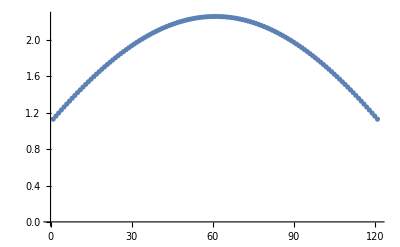

```mathematica
ListPlot[Table[Vsp[A,β,rad[x]]/.{θ->π/4,φ->π/4},{x,-60,60,1}]]
```

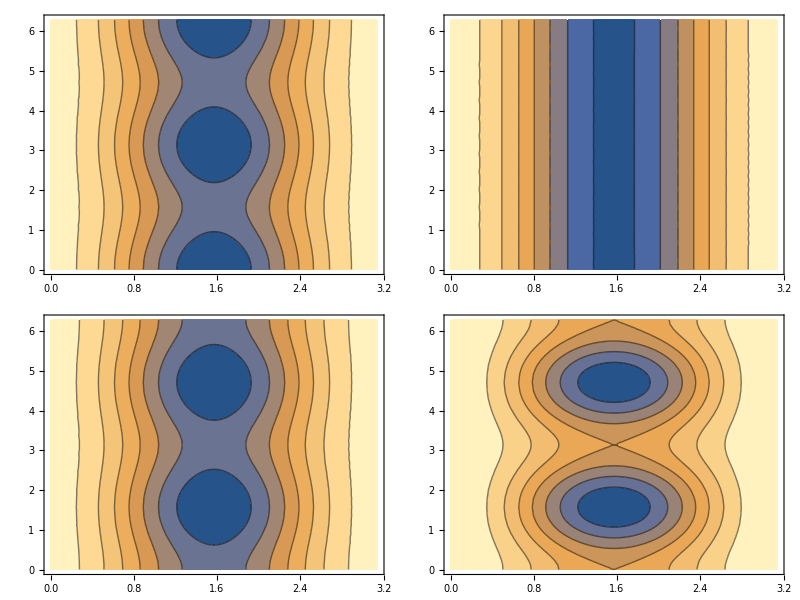

```mathematica
Grid[{{ContourPlot[Vsp[A,β,rad[-10]],{θ,0,π},{φ,0,2π}],ContourPlot[Vsp[A,β,rad[0]],{θ,0,π},{φ,0,2π}]},{ContourPlot[Vsp[A,β,rad[10]],{θ,0,π},{φ,0,2π}],ContourPlot[Vsp[A,β,rad[30]],{θ,0,π},{φ,0,2π}]}},Frame->All]
```

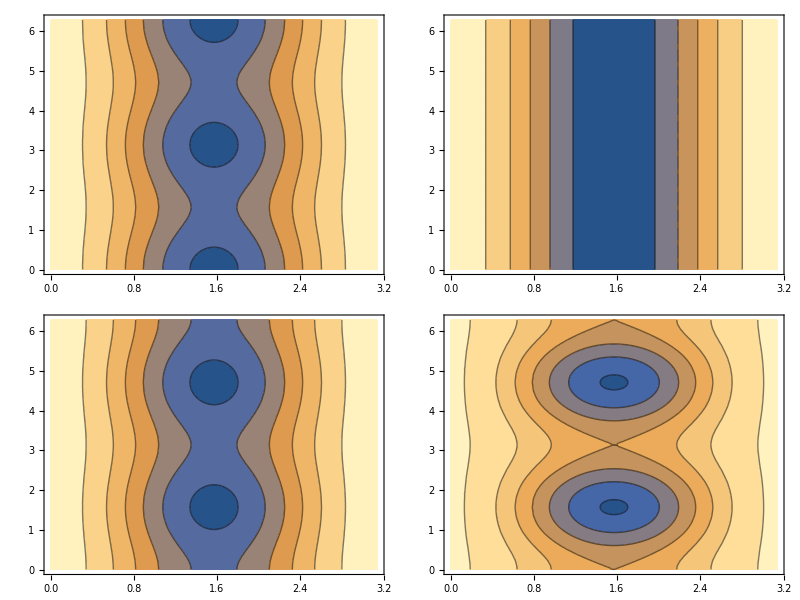

```mathematica
Grid[{{ContourPlot[Vsp[130,0.14,rad[-10]],{θ,0,π},{φ,0,2π}],ContourPlot[Vsp[130,0.14,rad[0]],{θ,0,π},{φ,0,2π}]},{ContourPlot[Vsp[130,0.14,rad[10]],{θ,0,π},{φ,0,2π}],ContourPlot[Vsp[130,0.14,rad[30]],{θ,0,π},{φ,0,2π}]}},Frame->All]
```

## Graphical representation of thge spherical harmonics for the triaxial potential -Graphics-

```mathematica
SphericalPlot3D[SphericalHarmonicY[2,0,θ,φ],{θ,0,π},{φ,0,2π}]
```

-Graphics3D-